```mathematica
a=2.41;
Nk=60;(*k-mesh will have Nk^2 points, Nk>1, integer*)
StringForm["The k-mesh has `` points.",Nk^2]
Λk=1; (*A factor controlling the size of the mesh in k space*)
Δk=Λk/Nk; (*Spacing between k-points*)
b=(4π)/(√3*a); (*Magnitude of reciprocal vectors*)
b1=b*{(-√3)/2,1/2}; (*Reciprocal vectors b1,b2*)
b2=b*{(√3)/2,1/2};
kk=1/3*(b1+2*b2);
kp=1/3*(b2+2*b1);
lineb1=Arrow[{{0,0},b1}]; 
lineb2=Arrow[{{0,0},b2}]; 
BZcontour = Polygon[{((4π)/(3a))*{-1,0},((4π)/(3a))*{(-1)/2,(√3)/2},((4π)/(3a))*{1/2,(√3)/2},((4π)/(3a))*{1,0},((4π)/(3a))*{1/2,(-√3)/2},((4π)/(3a))*{(-1)/2,(-√3)/2}}];
kaMesh=Flatten[Table[{(j-i)*Δk*b*((√3)/2),(j+i)*Δk*b*(1/2)},{i,1,Nk,1},{j,1,Nk,1}],1]; (*k-mesh first generated by reciprocal vectors *)
kaMesh1BZ=kaMesh-TensorProduct[(1-UnitStep[kaMesh.b2])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b1/b^2+0.5],b1]-TensorProduct[(1-UnitStep[kaMesh.b1])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b2/b^2+0.5],b2]-TensorProduct[UnitStep[kaMesh.b1]*UnitStep[kaMesh.b2]*Floor[kaMesh.(b1+b2)/b^2+0.5],(b1+b2)];
 (*Moving all k-points to 1BZ*)

FunkMesh[s_,t1_,t2_,x_]:=
Module[{kaMeshBZ},
kaMesh1BZaux=x;
(*Changing covered area of the 1BZ*)
kaMesh1BZ=kaMesh1BZaux*s;
(*MOVING K MESH TO K POINT*)
kaMesh1BZ=(kaMesh1BZᵀ+t1*{(4π)/(3a),0}+t2*(b1+b2))ᵀ;
kaMeshKpoint= kaMesh1BZ;
kaMesh1BZ= kaMesh1BZ-1*TensorProduct[Floor[kaMesh1BZ.(b1+b2)/b^2+0.5],(b1+b2)];
kaMesh1BZ=kaMesh1BZ-1*TensorProduct[(UnitStep[kaMesh1BZ[[All,2]]]*(UnitStep[kaMesh1BZ[[All,1]]]-UnitStep[-kaMesh1BZ[[All,1]]])+UnitStep[-kaMesh1BZ[[All,1]]])*Floor[kaMesh1BZ.b2/b^2+0.5],b2]-1*TensorProduct[(UnitStep[kaMesh1BZ[[All,2]]]*(UnitStep[-kaMesh1BZ[[All,1]]]-UnitStep[kaMesh1BZ[[All,1]]])+UnitStep[kaMesh1BZ[[All,1]]])*Floor[kaMesh1BZ.b1/b^2+0.5],b1]
]
```

The k-mesh has 3600 points.

```mathematica
FunPlot[s_,t1_,t2_]:=Show[ListPlot[{FunkMesh[s,t1,t2,kaMesh1BZ]},AspectRatio->Automatic,AxesLabel->{"kx","ky"},Epilog->{lineb1,lineb2,Text["b_2",b1+{0,0.2}],Text["b_1",b2+{0,0.2}],Text["1BZ",{0,-0.4}]},AspectRatio->Automatic,PlotMarkers->{Graphics[{Green,Disk[{0,0}]}],0.01},PlotStyle->Blue,PlotRange->{{-b,b},{-b,b}},Frame->True], Graphics[{Red,Opacity[0.0],EdgeForm [Dashed],Red,BZcontour}] 
]
```

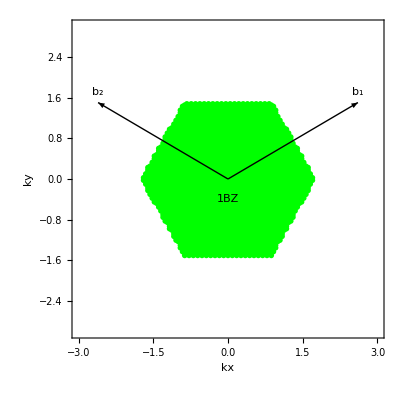

```mathematica
FunPlot[1.0,0.0,0.0]
```

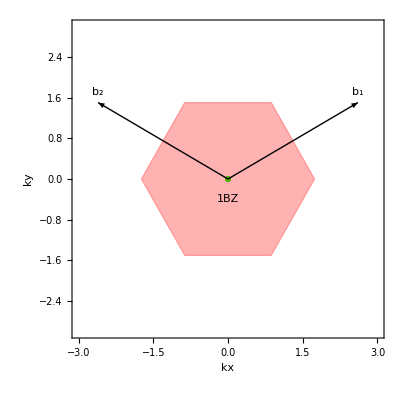
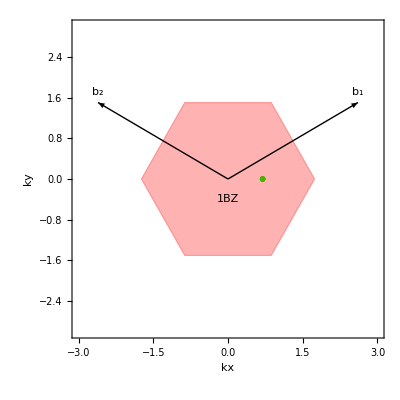
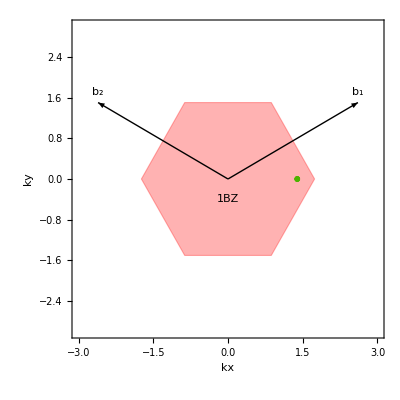
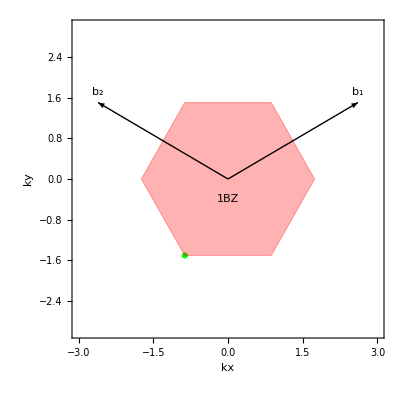

```mathematica
(*TRANSLATION FROM Γ TO K (In the direction of b1-b2)*)
Map[FunPlot[0.,#,0.]&,{0.,0.4,0.8,1.}]
```

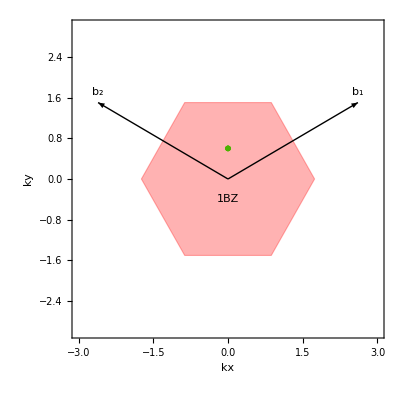
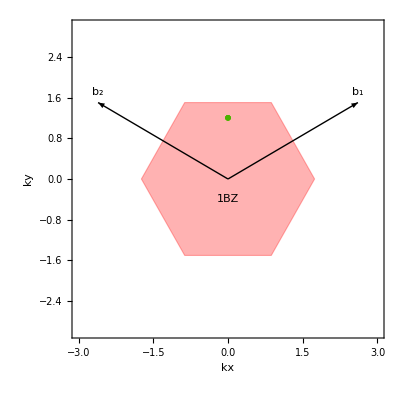
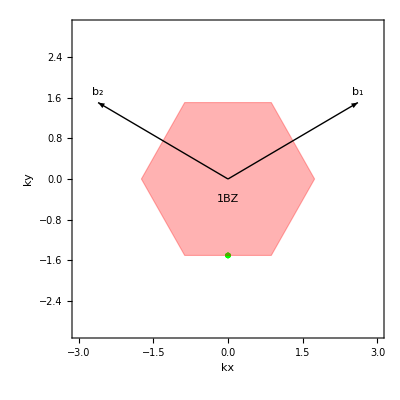
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*TRANSLATION FROM Γ TO M (In the direction of b3)*)
Map[FunPlot[0.,0.,#]&,{0.,0.2,0.4,.5}]
```

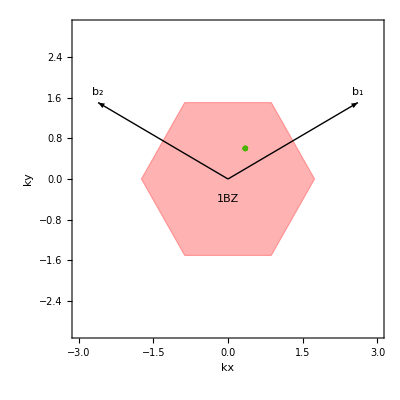
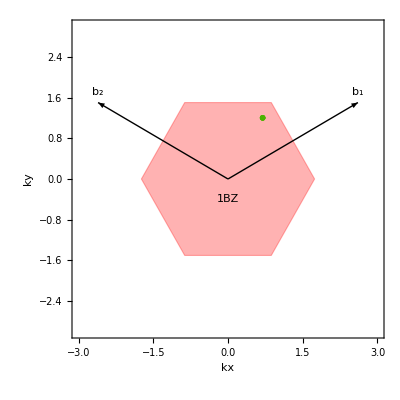
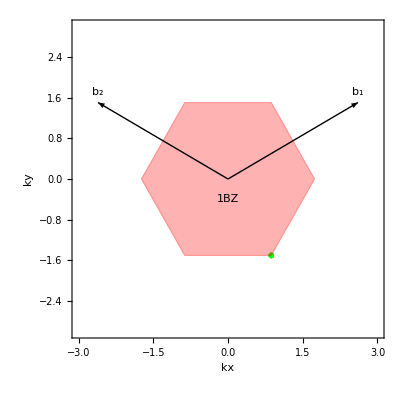
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*TRANSLATION IN THE DIRECTION OF K' (In the direction of b1 +b3)*)
Map[FunPlot[0.,#,#]&,{0.,0.2,0.4,.5}]
```